This is Mathematica notebook for simulating the fixation of ‘A2’ alleles under positive directional selection reported in “Positive feedback between demographic and selective fluctuations can greatly amplify the random fluctuation of population size” by Yuseob Kim

```mathematica
Rep=5; (* number of replicates *)
Cap=2000; (* total population size = filed + refuge *)
senv =0.2; sran=0.1; (* senv = a_S, sran = b_S *)
fenv=0.3; fran=0.1; (* fenv = a_U, fran = b_U *)
renv=0.05; rran=0.1; (* renv = a_V, rran = b_V *)
dregul=-1; (* dregul is parameter g in Kim (2023); a large positive value sets soft selection. A negative value sets hard selection *)
Lseq=4; (* the number of loci *)
NSelSite=4;  (* the number of loci under selection; as this study does not include neutral loci, you need to set Lseq = NSelSite *)
selco=Table[{0,1},{l,1,NSelSite}];
selco=Join[selco,Table[{0,0},{l,1,Lseq-NSelSite}]];
rmut=0.00002; (* mutation rate per locus per generation *)
rmig12=0.5; (* probability for a haploid in the field to move to the refuge in the migration step *)
rmig21=0.5;(* probability for a haploid in the refuge to move to the field in the migration step *)
rrec=0.01; (* recombination rate between adjacent loci per generation *)
TotGen=30000; (* maximum length (generation) of a single simulation run *)
intvl=1000;
cvlist={};
mTfix = {};
mfixed=Table[0,{l,1,NSelSite}];
nfixed=0;
For[rep=0,rep<Rep,rep++;
FFreqTraj={};
RFreqTraj={};
NPopTraj={};
PField={Cap/2};HField={0};
PRefuge={Cap/2};HRefuge={0}; (* simulation starts with individuals with haplotype 0 [= 000...0], Cap/2 each for the field and refuge *)
mHetTraj={};
allfixed=0;
gen=0;
fixed=Table[0,{l,1,NSelSite}];
AF=Table[0,{l,1,Lseq}];
fcount=0;
While[
(gen<TotGen)&&(allfixed==0),
gen++;
{PField,HField}=Mutation[PField,HField, rmut Lseq,Lseq]; (* mutation step in the field *)
{PField,HField}=Recombination[PField,HField,rrec Lseq,Lseq]; (* recombination step in the field *)
{PRefuge,HRefuge}=Mutation[PRefuge,HRefuge, rmut Lseq,Lseq];
{PRefuge,HRefuge}=Recombination[PRefuge,HRefuge,rrec Lseq,Lseq];
env=RandomVariate[NormalDistribution[]]; (* sampling Z_1 *)

HFitL=HaploFit[HField, AMFfitRF[env,senv, sran, selco,Lseq],Lseq]; (* sampling fitness for all haplotypes with positive frequencies *)
HFitLR=Table[1,{i,1,Length[HRefuge]}]; (* relative fitness is 1 for all haplotypes in the refuge *)
Kf=0.5Cap Exp[fenv env+fran RandomVariate[NormalDistribution[]]]; (* sampling the carrying capacity of the field *)
{PField,HField}=PoissonReproduceRF[PField, HField,HFitL, Kf, dregul]; (* reproduction in the field *)
Kr= 0.5Cap Exp[renv env+rran RandomVariate[NormalDistribution[]]];(* sampling the carrying capacity of the refuge *)
{PRefuge,HRefuge}=PoissonReproduceRF[PRefuge, HRefuge,HFitLR, Kr, dregul]; (* reproduction in the refuge *)

{PField,HField, PRefuge,HRefuge}=Migration[PField,HField,PRefuge,HRefuge,rmig12,rmig21];(* exchange of individuals between the field and refuge *)
NF=Total[PField];nHField=Length[PField];
NR=Total[PRefuge];nHRefuge=Length[PRefuge];
If[(NF==0)||(NR==0),Print[{gen,NF,NR}];Break[]];
FFreq=Table[Count1[PField, HField,nHField,site],{site,1,Lseq}]; (* counting individuals with '1' allele (= A2 allele) in the field *)
FFreqTraj=Append[FFreqTraj,FFreq];
RFreq=Table[Count1[PRefuge, HRefuge,nHRefuge,site],{site,1,Lseq}];
RFreqTraj=Append[RFreqTraj,RFreq];
NPopTraj=Append[NPopTraj,{NF,NR}];
For[site=0,site<Lseq,site++;
AF[[site]]=1.0(FFreq[[site]]+RFreq[[site]])/(NF+NR); (* allele frequency in the total population *)
If[fixed[[site]]==0,
If[AF[[site]]>0.9, fixed[[site]]=gen; fcount++] (* recording where and when the fixation of A2 allele occurred *)
]
];
If[fcount==NSelSite,allfixed=1];
If[Mod[gen,intvl]==0,
Print[{gen, AF}]
]
];
If[
gen<TotGen,
mTfix=Append[mTfix,Mean[fixed]]; (* recording the fixation times averaged over loci *)
fixed=Sort[fixed];
mfixed=mfixed+fixed;
nfixed++;
If[Lseq>1,
cv =1.0 StandardDeviation[fixed]/Mean[fixed]; (* coefficient of variation for fixation times *)
cvlist=Append[cvlist, cv],
cv=0
];
Print[rep,{gen,fixed}," cv= ", cv];
];
FreqDist=Append[FreqDist,AF];
];
TAllFix=gen;
vars=senv^2+sran^2;
covsf=senv fenv;
covsr=senv renv;
covfr=fenv renv;
If[vars>0,Phi =(covsf-covsr)/vars;Print["Phi=",Phi],Print["Neutral"]];
Print[cvlist];
Print[" mTfix = ", 1.0 Mean[mTfix]]; (* mean fixation time across replicates *)
If[Lseq>1,Print[ "mean cv = ", Mean[cvlist]]](* mean cv across replicates *)
```

{1000,{0.0840695,0.,0.966087,0.981761}}

1{1302,{883,913,1176,1302}} cv= 0.190785

{1000,{0.728876,0.,0.252021,0.113887}}

{2000,{1.,0.00156789,0.990279,1.}}

2{2497,{1023,1079,1097,2497}} cv= 0.502828

{1000,{0.37028,0.,0.,0.}}

{2000,{1.,1.,0.99936,0.0179257}}

3{2802,{1447,1539,1712,2802}} cv= 0.334767

4{875,{735,787,834,875}} cv= 0.0747424

{1000,{0.00595593,0.,0.,0.}}

{2000,{0.00532915,0.166144,0.,0.}}

{3000,{0.,0.912727,0.,0.290909}}

5{3618,{2461,3158,3494,3618}} cv= 0.163043

Phi=1.

{0.190785,0.502828,0.334767,0.0747424,0.163043}

mTfix = 1671.6

mean cv = 0.253233

Graphs below are generated for the last replicate of the above simulation

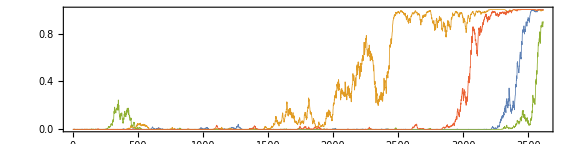

```mathematica
RelFreqList=Table[(FFreqTraj[[gen]][[site]]+RFreqTraj[[gen]][[site]])/Total[NPopTraj[[gen]]],{site,1,Lseq},{gen,1,TAllFix}];
gFreq=ListPlot[RelFreqList,Joined->True,Frame->True, PlotStyle->Thickness[0.001],PlotRange->{0,1},AspectRatio->0.25, ImageSize->Large](* plotting the A2 allele frequencies at all loci *)
```

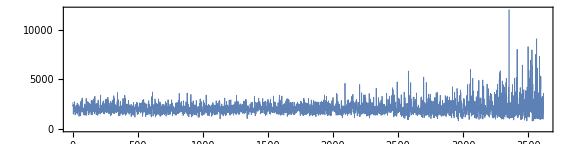

```mathematica
NPopList=Table[Total[NPopTraj[[gen]]],{gen,1,TAllFix}];
gNpop=ListPlot[NPopList,Joined->True,Frame->True, PlotStyle->Thickness[0.001],PlotRange->{0,12000},AspectRatio->0.25, ImageSize->Large] (* plotting total population size over time *)
```